```mathematica
ClearAll[print]
print[f_][x_]:=(Print@*f@x;x)
```

### Lab Calculations

```mathematica
a=3.5239;
λ=1.5418;
```

```mathematica
Subscript[d, hkl_]:=a/(√(Total@(IntegerDigits[hkl]^2)))
```

```mathematica
Table[
{n,hkl,
#(θ/.Solve[n λ==2 Subscript[d, hkl] Sin[θ °],θ])&/@{1,2}
},
{n,1,3},
{hkl,{111,200,220,311,222,400,331,420,422}}
]//TableForm
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

1 | 
111 | 
22.2661 | 44.5323 | 1 | 
200 | 
25.9462 | 51.8923 | 1 | 
220 | 
38.2254 | 76.4507 | 1 | 
311 | 
46.5151 | 93.0302 | 1 | 
222 | 
49.2722 | 98.5445 | 1 | 
400 | 
61.0513 | 122.103 | 1 | 
331 | 
72.4715 | 144.943 | 1 | 
420 | 
78.0529 | 156.106 | 1 | 
422 | 
90.-21.5718 ⅈ | 180.-43.1436 ⅈ
2 | 
111 | 
49.2722 | 98.5445 | 2 | 
200 | 
61.0513 | 122.103 | 2 | 
220 | 
90.-38.7468 ⅈ | 180.-77.4937 ⅈ | 2 | 
311 | 
90.-52.5602 ⅈ | 180.-105.12 ⅈ | 2 | 
222 | 
90.-55.9367 ⅈ | 180.-111.873 ⅈ | 2 | 
400 | 
90.-66.3992 ⅈ | 180.-132.798 ⅈ | 2 | 
331 | 
90.-72.2844 ⅈ | 180.-144.569 ⅈ | 2 | 
420 | 
90.-74.0019 ⅈ | 180.-148.004 ⅈ | 2 | 
422 | 
90.-79.989 ⅈ | 180.-159.978 ⅈ
3 | 
111 | 
90.-29.6303 ⅈ | 180.-59.2607 ⅈ | 3 | 
200 | 
90.-44.198 ⅈ | 180.-88.3961 ⅈ | 3 | 
220 | 
90.-70.4558 ⅈ | 180.-140.912 ⅈ | 3 | 
311 | 
90.-80.9836 ⅈ | 180.-161.967 ⅈ | 3 | 
222 | 
90.-83.7743 ⅈ | 180.-167.549 ⅈ | 3 | 
400 | 
90.-92.8113 ⅈ | 180.-185.623 ⅈ | 3 | 
331 | 
90.-98.0997 ⅈ | 180.-196.199 ⅈ | 3 | 
420 | 
90.-99.6653 ⅈ | 180.-199.331 ⅈ | 3 | 
422 | 
90.-105.19 ⅈ | 180.-210.38 ⅈ

```mathematica
VernierFormat2`VernierFormat2Import[filename_String,options___]:=Module[
{stream,head,data},
stream=OpenRead[filename];
head=ReadList[stream,"String",7];
data=Partition[ReadList[stream,"Number"],2];
Close[stream];
{
"Header"->head,
"Data"->data
}
]
```

```mathematica
ImportExport`RegisterImport[
"VernierFormat2",
VernierFormat2`VernierFormat2Import
]
```

```mathematica
hklLookupTable={{100, 110, 111, 200, 210, 211, {}, 220, {300,221}, 310, 311, 222, 320, 321, {}, 400, {410,322}, {411,330}, 331, 420, 421, 332, {}, 422, {500,430}}}[[1]]//print@Length;
```

25

### Analysis

```mathematica
Table[
StringSplit[FileNameSplit[path][[-1]],".txt"],
{path,{"C:\\Users\\andre\\Documents\\Rutgers\\S23\\388\\X-Ray\\XRayLab\\NiSi55_42.2_Fine.txt","C:\\Users\\andre\\Documents\\Rutgers\\S23\\388\\X-Ray\\XRayLab\\Ni74Cu26_50_43_Fine.txt"}}
]//TableForm
```

NiSi55_42.2_Fine
Ni74Cu26_50_43_Fine

```mathematica
dataFiles=FileNames["*.txt",NotebookDirectory[]<>"XRayLab"]//print@TableForm;
data=Table[{StringSplit[FileNameSplit[path][[-1]],"."][[1]],Import[path,{"VernierFormat2","Data"}]},{path,dataFiles}];
```

C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CANickel1979_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CANickel1984_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi160_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\CuSi54_40_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni18Cu82_48_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni47Cu53_48_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Ni74Cu26_50_43_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi100_70.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi130_120.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi160_140.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi55_42.125_Fine.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\NiSi60_40.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Silicon80_20.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\Unknown50min_160_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\UnknownLast30Min_63_0.txt
C:\Users\andre\Documents\Rutgers\S23\388\X-Ray\XRayLab\USNickel_50_43_Fine.txt

```mathematica
fullSpeed=Table[!StringContainsQ[file,"Fine"],{file,dataFiles}];
slope=1/2+3/2 Boole@fullSpeed
measurementAngles=Table[
ToExpression/@StringTrim[Take[StringSplit[StringSplit[FileNameSplit[file][[-1]],".txt"][[1]],"_"]/."Fine"|"det"->Nothing,-2],Except@DigitCharacter..],
{file,dataFiles}
]
minToAngle[i_][min_]:=measurementAngles[[i,1]]-slope[[i]]min
angles=Table[minToAngle[i]/@data[[i,2,;;,1]],{i,Length@data}];
data=Table[{data[[i,1]],{angles[[i]]/2,data[[i,2,;;,2]]}ᵀ},{i,Length@data}];
TableForm[Table[{it[[4]],(Subtract@@it[[1]])/it[[2]]//N,it[[3]]/((Subtract@@it[[1]])/it[[2]])//N,0.025it[[3]]},{it,{measurementAngles,slope,Length/@data[[;;,2]],data[[;;,1]]}ᵀ}],TableHeadings->{None,{"Run","Minutes","Samples/Min","Window Size"}}]
```

{1/2,1/2,2,1/2,1/2,1/2,1/2,2,2,2,1/2,2,2,2,2,1/2}

{{50,43},{50,43},{160,0},{54,40},{48,43},{48,43},{50,43},{100,70},{130,120},{160,140},{55,42.125},{60,40},{80,20},{160,0},{63,0},{50,43}}

Run | Minutes | Samples/Min | Window Size
CANickel1979_50_43_Fine | 14. | 20. | 7.
CANickel1984_50_43_Fine | 14. | 20. | 7.
CuSi160_0 | 80. | 20. | 40.
CuSi54_40_Fine | 28. | 20. | 14.
Ni18Cu82_48_43_Fine | 10. | 20. | 5.
Ni47Cu53_48_43_Fine | 10. | 20. | 5.
Ni74Cu26_50_43_Fine | 14. | 20. | 7.
NiSi100_70 | 15. | 30. | 11.25
NiSi130_120 | 5. | 30. | 3.75
NiSi160_140 | 10. | 30. | 7.5
NiSi55_42 | 25.75 | 20. | 12.875
NiSi60_40 | 10. | 30. | 7.5
Silicon80_20 | 30. | 10. | 7.5
Unknown50min_160_0 | 80. | 20. | 40.
UnknownLast30Min_63_0 | 31.5 | 20. | 15.75
USNickel_50_43_Fine | 14. | 20. | 7.

```mathematica
N@(1/40)
```

0.025

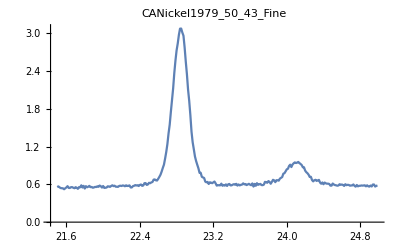
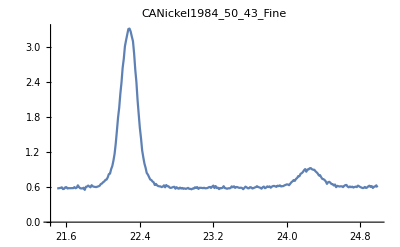
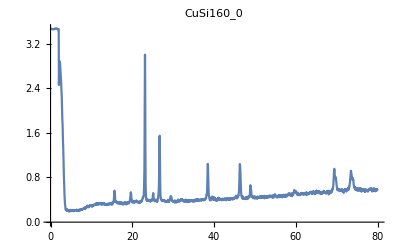
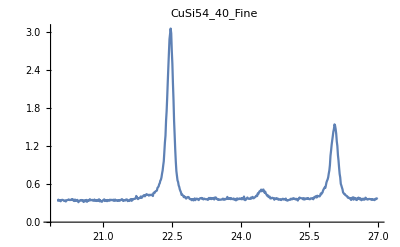
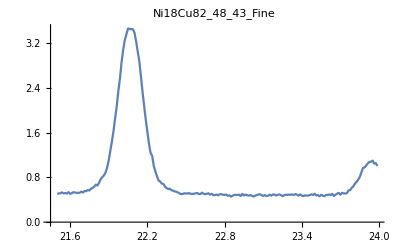
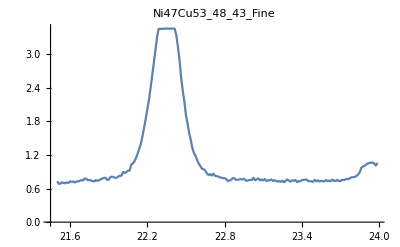
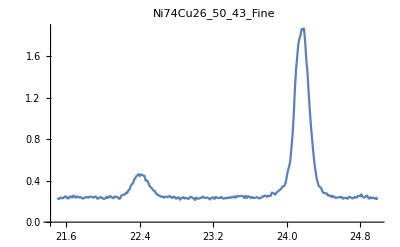
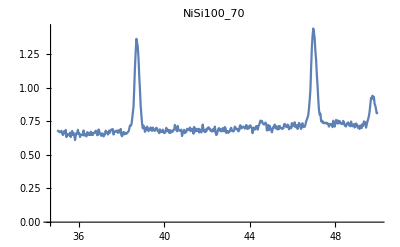

```mathematica
Table[ListPlot[datum[[2]],PlotLabel->datum[[1]],Joined->True,PlotRange->Full],{datum,data}]
```

#### Peak finding for each run

each run has different parameters needed to find all the peaks

```mathematica
peaks={{FindPeaks[data1[[;;,2]],1.5,0.01]}, {2}, {3}}
```

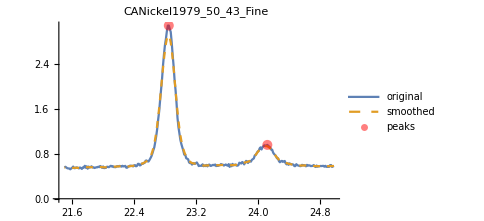
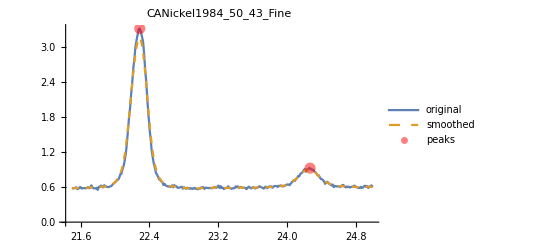
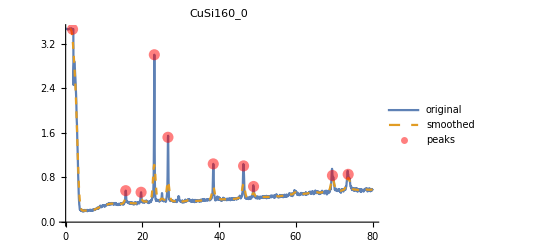
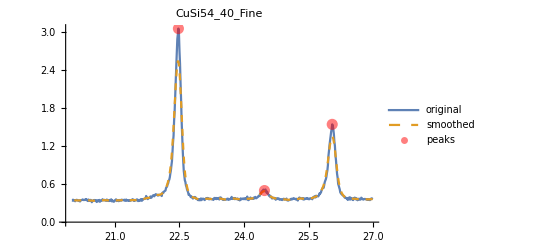
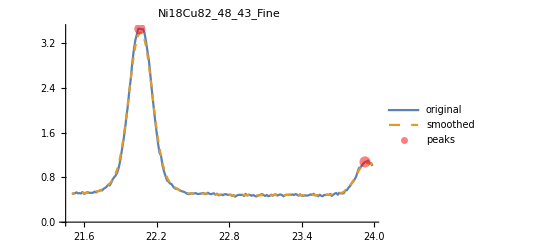
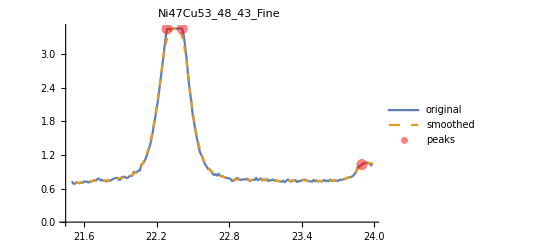
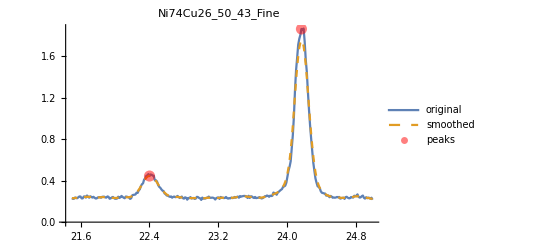
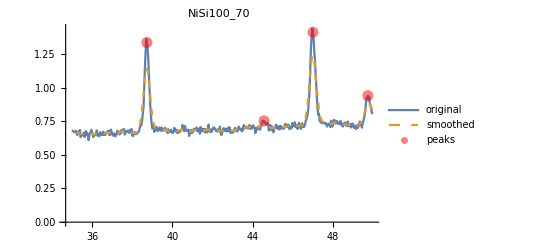
-Graphics- | θ | V
24.125 | 0.95625
22.85 | 3.075
-Graphics- | θ | V
24.2625 | 0.9225
22.2875 | 3.3075
-Graphics- | θ | V
73.6 | 0.85625
69.5 | 0.835
48.95 | 0.63875
46.35 | 1.0075
38.45 | 1.04375
26.65 | 1.52
23.1 | 2.99875
19.65 | 0.535
15.65 | 0.56375
1.8 | 3.455
-Graphics- | θ | V
26.05 | 1.54
24.475 | 0.4975
22.475 | 3.04875
-Graphics- | θ | V
23.925 | 1.0775
22.0625 | 3.45875
-Graphics- | θ | V
23.9 | 1.0275
22.4125 | 3.45125
22.2875 | 3.4475
-Graphics- | θ | V
24.1625 | 1.86
22.4 | 0.44375
-Graphics- | θ | V
49.7333 | 0.94
47. | 1.41125
44.5667 | 0.7525
38.7333 | 1.335
-Graphics- | θ | V
64.5667 | 0.86875
64.2 | 0.8475
63.7333 | 0.85875
63.0667 | 0.85
62.4333 | 0.8125
61.7333 | 0.91125
61.4667 | 0.90125
61.1 | 0.82125
60.4333 | 0.80625
60.0667 | 0.795
-Graphics- | θ | V
79. | 1.215
78.3333 | 1.4225
73.3333 | 1.16625
72.8333 | 1.3675
-Graphics- | θ | V
26.4875 | 2.0475
24.2375 | 0.8725
22.8 | 3.44875
-Graphics- | θ | V
26.0333 | 1.65
23.7667 | 0.785
22.3333 | 2.595
-Graphics- | θ | V
38.2 | 0.36375
34.5 | 0.2725
28. | 0.62875
23.5 | 0.765
14.1 | 1.06375
-Graphics- | θ | V
78.85 | 0.37375
66.9 | 1.32
51.25 | 1.14625
44.35 | 1.26
37.35 | 1.45
30.8 | 0.21875
-Graphics- | θ | V
29.45 | 1.1175
20.35 | 3.4925
1.75 | 2.885
-Graphics- | θ | V
24.05 | 1.47625
22.2125 | 3.08625

```mathematica
σ=5;
Table[Module[
{title,runAngles,runVoltages,filterRadius,σ,runVoltagesSmooth,runDataSmooth,n,ker,convolved,s,peakIdx,peakV,peakAngle,peaks,plot,table},
{title,runData}=runData;
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles];
σ=√filterRadius;
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
n=filterRadius;
ker=Join[Table[1,n],{-2n},Table[1,n]];
convolved=ListConvolve[ker,ArrayPad[runVoltagesSmooth,n,"Extrapolated"]];
(*convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];*)
(*s=0.0006;*)
s=StandardDeviation@convolved/3;
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ;
peakAngle=runAngles[[peakIdx]];
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
plot=ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"original","smoothed","peaks"},
PlotLabel->title
];
table=TableForm[peaks,TableHeadings->{None, {"θ","V"}}];
{plot,table}
],
{runData,data}
]//TableForm
```

```mathematica
runData=data[[1,2]];
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles]//print@Identity;
σ=filterRadius/2//print@N@*Identity;
(*σ=√filterRadius//print@N@*Identity;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
s=0.0006;
s=StandardDeviation@convolved/3
```

7

3.5

0.00248099

```mathematica
getAngles[data_,index_]:=;
getAngles[data_,indices_]:=;
```

```mathematica
{peakIdx,peakV}=FindPeaks[runVoltagesSmooth]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

```mathematica
{peakIdx,peakV}=Select[-#[[2]]<-s&][FindPeaks[-convolved]]ᵀ
peakAngle=runAngles[[peakIdx]]
peakV=runVoltages[[peakIdx]];
peaks={peakAngle,peakV}ᵀ;
```

{{71,172},{0.00413758,0.0401199}}

{20.257,20.1781}

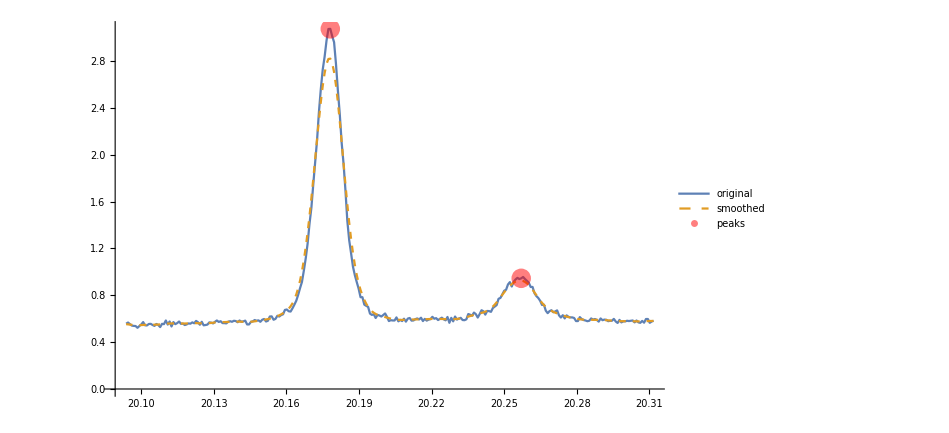

```mathematica
ListPlot[
{runData,runDataSmooth,peaks},
Joined->{True,True,False},
PlotStyle->{Automatic,Dashed,Directive[Red,PointSize[.02],Opacity[0.5]]},
PlotRange->Full,
PlotLegends->{"original","smoothed","peaks"}
]
```

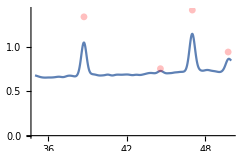

```mathematica
ListPlot[
{runDataSmooth,peaks},
Joined->{True,False},
PlotStyle->{Automatic,Directive[Red,PointSize[.02],Opacity[0.25]]},
PlotRange->Full
]
```

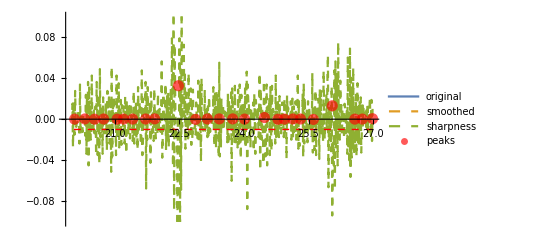

```mathematica
sharpness={runAngles,ListConvolve[{1,-2,1},ArrayPad[runVoltages,1,"Reversed"]]}ᵀ;
ListLinePlot[
{runData,runDataSmooth,sharpness,peaks},
Joined->{True,True,True,False},
PlotStyle->{Automatic,Dashed,Dashed,{Directive[Red,PointSize[.02],Opacity[0.65]]}},
PlotLegends->{"original","smoothed","sharpness","peaks"},
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-0.01},{runAngles[[-1]],-0.01}}]},
PlotRange->{-.1,.1}
]
```

0.00248099

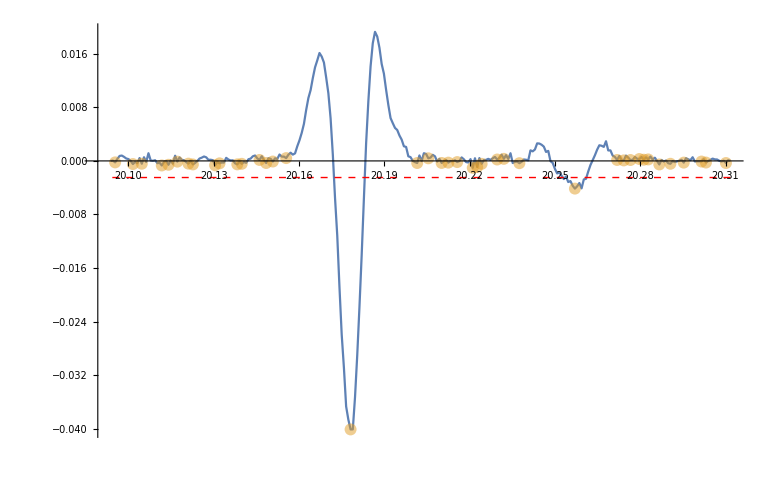

```mathematica
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation[convolved]/3//N
(*s=(StandardDeviation@convolved/print@Identity)/3*)
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
```

5

2.5

{1,1,1,1,1,-10,1,1,1,1,1}

0.153381

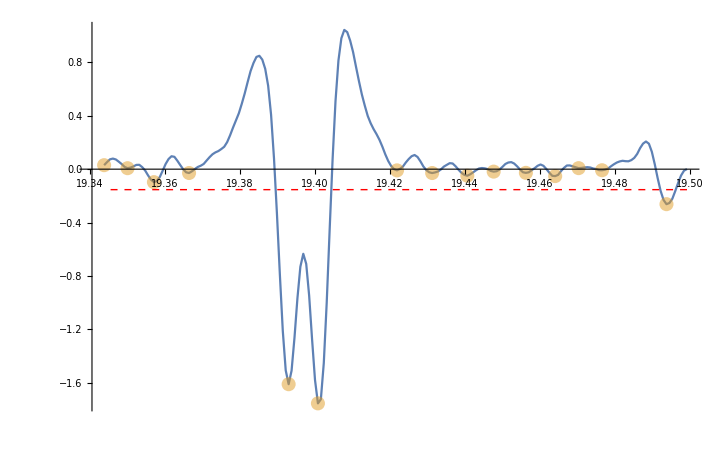

```mathematica
runData=data[[6,2]];
{runAngles,runVoltages}=runDataᵀ;
filterRadius=Ceiling[1/40 Length@runAngles]//print@Identity;
σ=filterRadius/2//print@N@*Identity;
(*σ=√filterRadius//print@N@*Identity;*)
runVoltagesSmooth=GaussianFilter[runVoltages,{filterRadius,σ}];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
n=filterRadius;
ker=Join[Table[1,n],{-2n},Table[1,n]]
convolved=ListConvolve[ker,ArrayPad[runVoltagesSmooth,n,"Extrapolated"]];
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation[convolved]/3
(*s=(StandardDeviation@convolved/print@Identity)/3*)
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
```

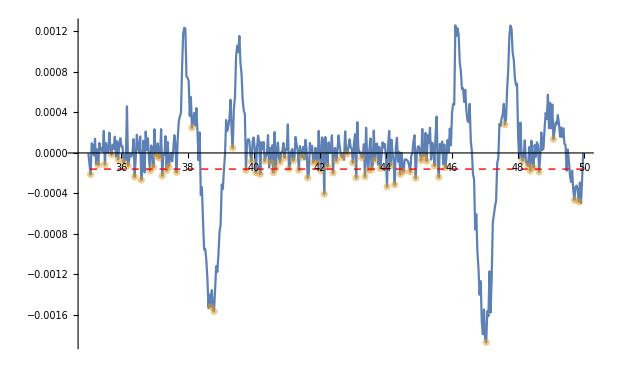

```mathematica
Table[
Module[
{},
runData=data[[6,2]];
{runAngles,runVoltages}=runDataᵀ;
σ=6;
filterRadius=Ceiling@*Sqrt@*Length@runAngles;
runVoltagesSmooth=GaussianFilter[runVoltages,filterRadius];
runDataSmooth={runAngles,runVoltagesSmooth}ᵀ;
convolved=ListConvolve[{1,-2,1},ArrayPad[runVoltagesSmooth,1,"Extrapolated"]];
sharpness={runAngles,convolved}ᵀ;
{peakIdx,peakV}=FindPeaks[-convolved]ᵀ;
peakAngle=runAngles[[peakIdx]];
peaks={peakAngle,-peakV}ᵀ;
s=0.0006;
s=StandardDeviation@convolved/3;
ListLinePlot[
{sharpness,peaks},
Joined->{True,False},
PlotRange->Full,
Epilog->{Dashed,Red,Line[{{runAngles[[1]],-s},{runAngles[[-1]],-s}}]},
PlotRange->{-.1,.1},
PlotStyle->{Automatic,Opacity@.5}
]
],
{i,1,1}
]
```

```mathematica
data1[[2]]
```

{26.975,0.37375}

```mathematica
GaussianFilter[data1[[2]],{3,1.5}]
```

{17.5865,9.76229}